```mathematica
raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/results.json"];
raw = Association[#]&/@raw
```

{<|quadErrorSigma→0.00005,iteration→0,magnetConfigKey→upstream,M5FF_xCenter→0.000187636,M5FF_yCenter→-0.000132686,IPOTR1_xCenter→0.000339168,IPOTR1_yCenter→0.0000419181,PENT_xCenter→0.000341573,PENT_yCenter→0.0000446896,IPOTR2_xCenter→0.000414934,IPOTR2_yCenter→0.00012922,M0EX_xCenter→0.000716197,M0EX_yCenter→0.000251692|>,<|quadErrorSigma→0.00005,iteration→0,magnetConfigKey→PENT,M5FF_xCenter→0.000163002,M5FF_yCenter→-0.00014517,IPOTR1_xCenter→0.000315285,IPOTR1_yCenter→9.3371×10^-6,PENT_xCenter→0.000317702,PENT_yCenter→0.0000117896,IPOTR2_xCenter→0.000391426,IPOTR2_yCenter→0.0000865906,M0EX_xCenter→0.000687316,M0EX_yCenter→0.000201882|>,<|quadErrorSigma→0.00005,iteration→0,magnetConfigKey→downstream,M5FF_xCenter→0.000141429,M5FF_yCenter→-0.00015654,IPOTR1_xCenter→0.00029498,IPOTR1_yCenter→-0.0000173017,PENT_xCenter→0.000297417,PENT_yCenter→-0.0000150916,IPOTR2_xCenter→0.000371755,IPOTR2_yCenter→0.0000523173,M0EX_xCenter→0.000663952,M0EX_yCenter→0.000162623|>,<|quadErrorSigma→0.00005,iteration→1,magnetConfigKey→upstream,M5FF_xCenter→0.000015604,M5FF_yCenter→0.000143467,IPOTR1_xCenter→0.0000394182,IPOTR1_yCenter→0.000398038,PENT_xCenter→0.0000397962,PENT_yCenter→0.000402079,IPOTR2_xCenter→0.0000513253,IPOTR2_yCenter→0.000525324,M0EX_xCenter→0.0000949424,M0EX_yCenter→0.000619934|>,<|quadErrorSigma→0.00005,iteration→1,magnetConfigKey→PENT,M5FF_xCenter→0.0000184156,M5FF_yCenter→0.000143529,IPOTR1_xCenter→0.0000412802,IPOTR1_yCenter→0.000383142,PENT_xCenter→0.0000416431,PENT_yCenter→0.000386945,IPOTR2_xCenter→0.0000527125,IPOTR2_yCenter→0.000502948,M0EX_xCenter→0.0000955123,M0EX_yCenter→0.000589884|>,<|quadErrorSigma→0.00005,iteration→1,magnetConfigKey→downstream,M5FF_xCenter→0.0000209112,M5FF_yCenter→0.000143524,IPOTR1_xCenter→0.0000430459,IPOTR1_yCenter→0.000370527,PENT_xCenter→0.0000433973,PENT_yCenter→0.00037413,IPOTR2_xCenter→0.0000541133,IPOTR2_yCenter→0.000484028,M0EX_xCenter→0.0000963749,M0EX_yCenter→0.000564507|>,<|quadErrorSigma→0.00005,iteration→2,magnetConfigKey→upstream,M5FF_xCenter→0.0000311112,M5FF_yCenter→-0.0000697773,IPOTR1_xCenter→0.000220869,IPOTR1_yCenter→-0.000164514,PENT_xCenter→0.000223881,PENT_yCenter→-0.000166017,IPOTR2_xCenter→0.000315748,IPOTR2_yCenter→-0.000211882,M0EX_xCenter→0.000638266,M0EX_yCenter→-0.000243007|>,<|quadErrorSigma→0.00005,iteration→2,magnetConfigKey→PENT,M5FF_xCenter→-4.0397×10^-6,M5FF_yCenter→-0.000069133,IPOTR1_xCenter→0.000182609,IPOTR1_yCenter→-0.000161938,PENT_xCenter→0.000185571,PENT_yCenter→-0.000163412,IPOTR2_xCenter→0.000275933,IPOTR2_yCenter→-0.000208341,M0EX_xCenter→0.000583864,M0EX_yCenter→-0.000238638|>,<|quadErrorSigma→0.00005,iteration→2,magnetConfigKey→downstream,M5FF_xCenter→-0.000030533,M5FF_yCenter→-0.0000679338,IPOTR1_xCenter→0.000152238,IPOTR1_yCenter→-0.000159206,PENT_xCenter→0.000155139,PENT_yCenter→-0.000160655,IPOTR2_xCenter→0.000243623,IPOTR2_yCenter→-0.000204842,M0EX_xCenter→0.00053802,M0EX_yCenter→-0.000234652|>,<|quadErrorSigma→0.00005,iteration→3,magnetConfigKey→upstream,M5FF_xCenter→-0.0000231375,M5FF_yCenter→-0.000203318,IPOTR1_xCenter→-0.000106184,IPOTR1_yCenter→0.000288241,PENT_xCenter→-0.000107502,PENT_yCenter→0.000296044,IPOTR2_xCenter→-0.000147706,IPOTR2_yCenter→0.00053402,M0EX_xCenter→-0.000291411,M0EX_yCenter→0.000836395|>,<|quadErrorSigma→0.00005,iteration→3,magnetConfigKey→PENT,M5FF_xCenter→-0.0000107493,M5FF_yCenter→-0.000236407,IPOTR1_xCenter→-0.0000924519,IPOTR1_yCenter→0.000212566,PENT_xCenter→-0.0000937488,PENT_yCenter→0.000219692,IPOTR2_xCenter→-0.000133303,IPOTR2_yCenter→0.000437052,M0EX_xCenter→-0.000271457,M0EX_yCenter→0.000725864|>,<|quadErrorSigma→0.00005,iteration→3,magnetConfigKey→downstream,M5FF_xCenter→-2.0276×10^-6,M5FF_yCenter→-0.000264553,IPOTR1_xCenter→-0.0000824551,IPOTR1_yCenter→0.00014875,PENT_xCenter→-0.0000837317,PENT_yCenter→0.00015531,IPOTR2_xCenter→-0.000122669,IPOTR2_yCenter→0.000355401,M0EX_xCenter→-0.000256369,M0EX_yCenter→0.000632961|>,<|quadErrorSigma→0.00005,iteration→4,magnetConfigKey→upstream,M5FF_xCenter→0.000212414,M5FF_yCenter→-0.0000103162,IPOTR1_xCenter→0.00020461,IPOTR1_yCenter→-0.000146991,PENT_xCenter→0.000204486,PENT_yCenter→-0.00014916,IPOTR2_xCenter→0.000200707,IPOTR2_yCenter→-0.000215328,M0EX_xCenter→0.000244825,M0EX_yCenter→-0.000282745|>,<|quadErrorSigma→0.00005,iteration→4,magnetConfigKey→PENT,M5FF_xCenter→0.000212269,M5FF_yCenter→-6.4554×10^-6,IPOTR1_xCenter→0.000208533,IPOTR1_yCenter→-0.000132085,PENT_xCenter→0.000208473,PENT_yCenter→-0.000134079,IPOTR2_xCenter→0.000206664,IPOTR2_yCenter→-0.000194899,M0EX_xCenter→0.000257478,M0EX_yCenter→-0.000257622|>,<|quadErrorSigma→0.00005,iteration→4,magnetConfigKey→downstream,M5FF_xCenter→0.00020993,M5FF_yCenter→-4.3762×10^-6,IPOTR1_xCenter→0.000211374,IPOTR1_yCenter→-0.000120179,PENT_xCenter→0.000211397,PENT_yCenter→-0.000122017,IPOTR2_xCenter→0.000212097,IPOTR2_yCenter→-0.000178081,M0EX_xCenter→0.00027086,M0EX_yCenter→-0.00023629|>}

```mathematica
activeData = Select[raw,#iteration == 0&];
```

```mathematica
plotFunc[data_,label_]:=(
ListPlot[{#}&/@data,PlotRange->{{-800,800},{-800,800}},AspectRatio->1,ImageSize->800,LabelStyle->20,PlotLabel->label]
)
```

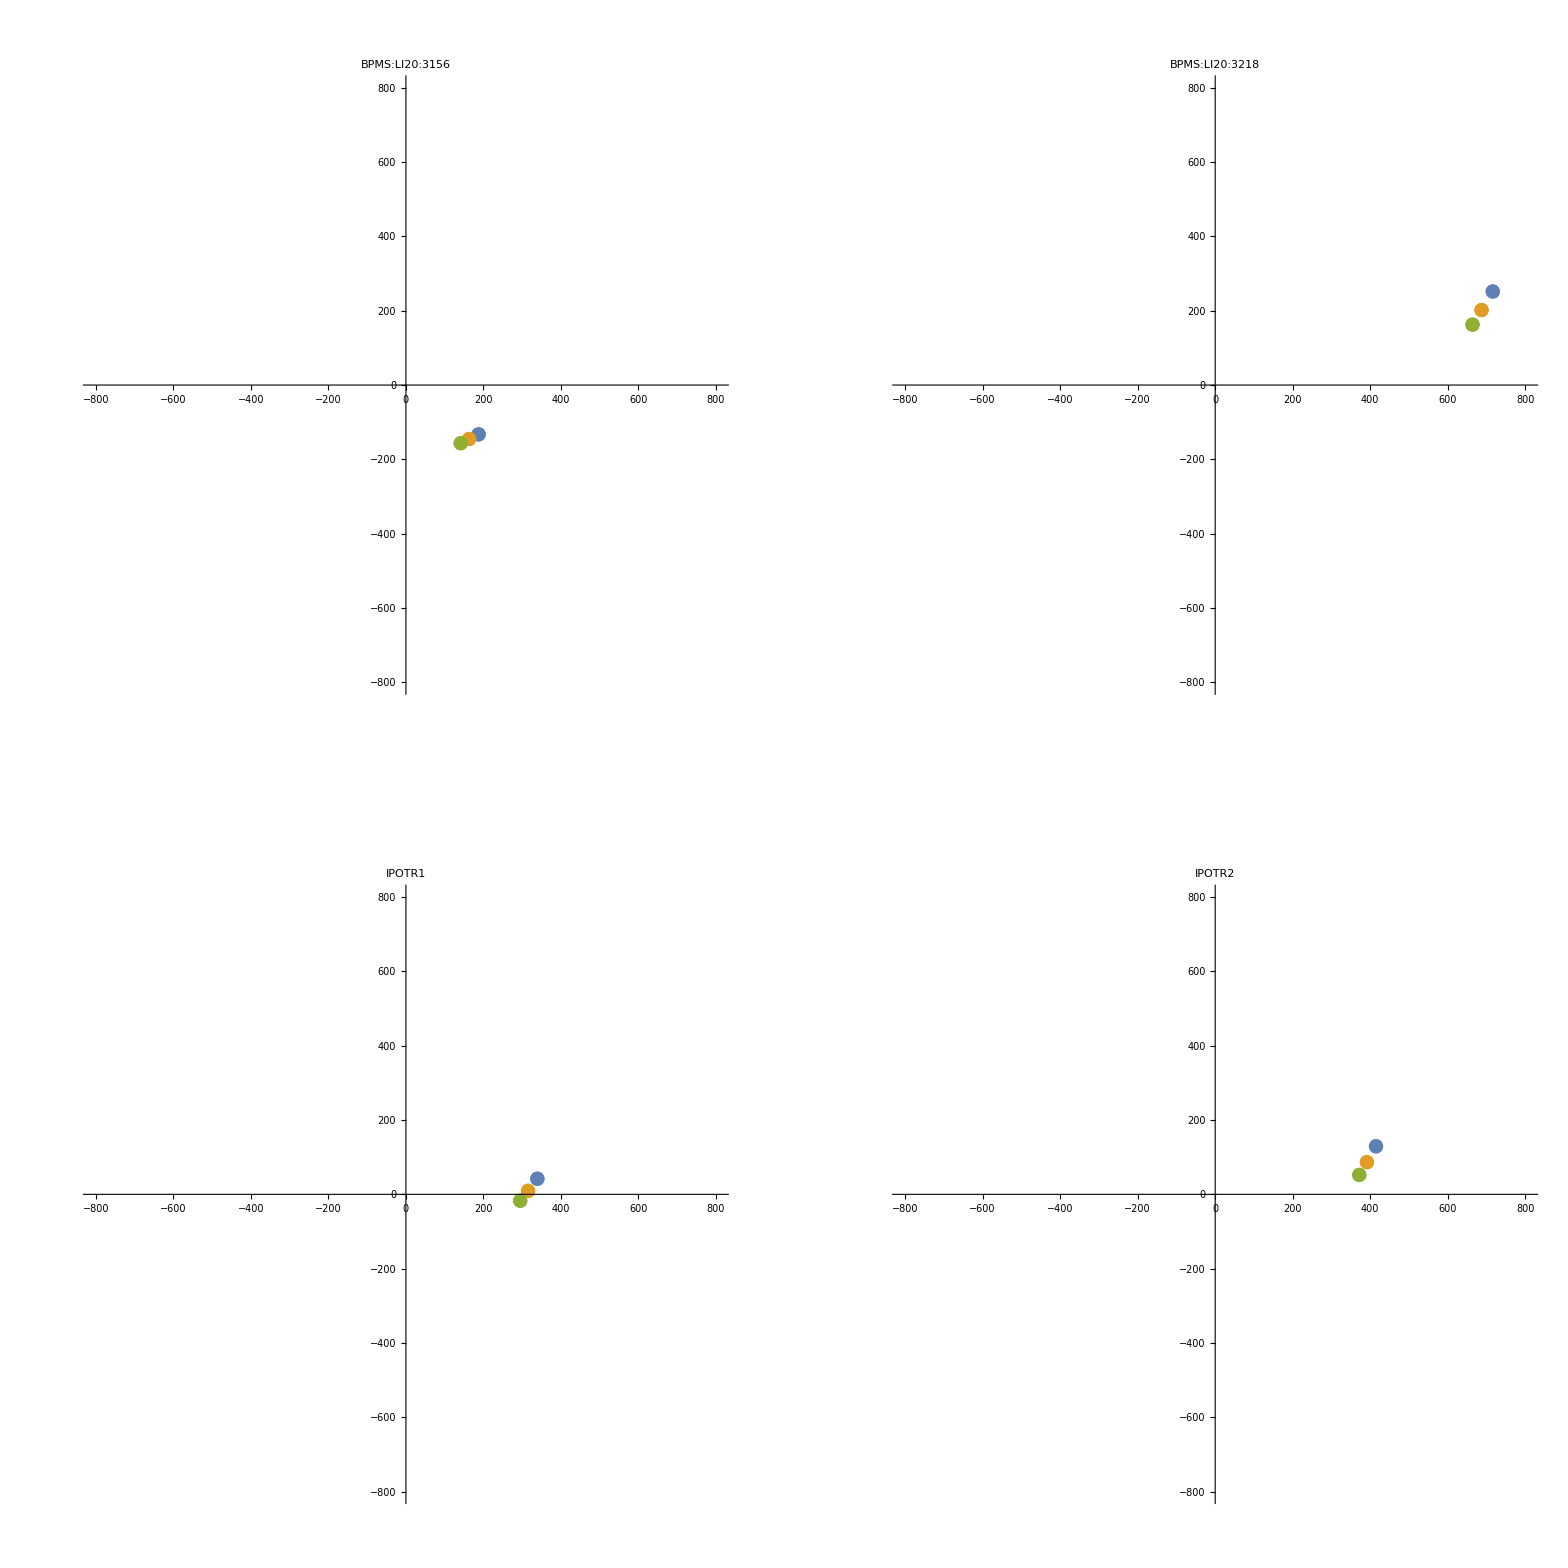

```mathematica
GraphicsGrid[{{
plotFunc[
10^6{#["M5FF_xCenter"],#["M5FF_yCenter"]}&/@activeData,
"BPMS:LI20:3156"
],
plotFunc[
10^6{#["M0EX_xCenter"],#["M0EX_yCenter"]}&/@activeData,
"BPMS:LI20:3218"
]
},{
plotFunc[
10^6{#["IPOTR1_xCenter"],#["IPOTR1_yCenter"]}&/@activeData,
"IPOTR1"
],
plotFunc[
10^6{#["IPOTR2_xCenter"],#["IPOTR2_yCenter"]}&/@activeData,
"IPOTR2"
]

}
},
ImageSize->1600]
```